```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/lorenzo/Phi4

```mathematica
m=1;
L=14;
ω[k_]:=Sqrt[m^2+k^2]
energy[klist_]:=Plus@@Map[ω,klist]
```

## g = 0.0001

```mathematica
(* Here I import the "discretized" wave function, after having appropriately "normalized" it
according to the occupation numbers and to the quantum numbers of the states *)
v =Import["data/wf3p_g=0.0001_L=14_E=20_nmax=3.csv","Data"];
data=ArrayReshape[v,{Length[v⟦1⟧]/3,3}];
data2=Select[data,(#⟦1⟧≥ 0)&];
```

```mathematica
(*Compare with the perturbative analytical wave function *)
pertWf[k1_,k2_,k3_]:=1/(m-(ω[k1]+ω[k2]+ω[k3]))1/Sqrt[ω[k1]ω[k2]ω[k3]m]
fit=Fit[data, pertWf[k1,k2,-k1-k2],{k1,k2}];
```

```mathematica
Show[Plot3D[fit,{k1,-3,3},{k2,-3,3}],ListPointPlot3D[data,PlotStyle->PointSize[0.01]]]
```

-Graphics3D-

## g = 1

```mathematica
v =Import["data/wf3p_g=1_L=14_E=20_nmax=5.csv","Data"];
data=ArrayReshape[v,{Length[v⟦1⟧]/3,3}];
data2=Select[data,(#⟦1⟧≥ 0)&];
ListPointPlot3D[data]
(* We see that the function is smooth apart from the points k1=0, k2=0,k1+k2=0 *)
```

-Graphics3D-

## Ansatz

```mathematica
(* High-energy part of the wave function *)
Emax = 7;
wfh = Select[data,energy[#⟦1⟧,#⟦2⟧,-#⟦1⟧-#⟦2⟧]≥Emax&];
ListPointPlot3D[wfh,PlotRange-> All]
```

-Graphics3D-

```mathematica
(* Ansatz for the tails *)
tailsNonSym={
1/energy[k1,k2,k3] 1/Sqrt[ω[k1]ω[k2]ω[k3]],
1/energy[k1,k2,k3]^2 1/Sqrt[ω[k1]ω[k2]ω[k3]]^2,
1/energy[k1,k2,k3]^3 1/Sqrt[ω[k1]ω[k2]ω[k3]]^3
(*,1/energy[k1,k2,k3] 1/Sqrt[ω[k1]ω[k2]ω[k3]]E^(-L^2 k1^2),
1/energy[k1,k2,k3] 1/Sqrt[ω[k1]ω[k2]ω[k3]]E^(-2L^2 k1^2)*)
};
(* Symmetrize w.r.t. momenta *)
symmetrize[expr_]:=Sum[expr/.{k1-> q⟦1⟧,k2-> q⟦2⟧,k3-> q⟦3⟧},{q,Permutations[{k1,k2,k3}]}]
tails=Map[symmetrize,tailsNonSym];
```

```mathematica
fit=Fit[wfh,tails/.{k3-> -k1-k2},{k1,k2}];
Show[
Plot3D[fit,{k1,-5,5},{k2,-5,5},PlotRange->{-0.003,0.}],
ListPointPlot3D[wfh]
]
```

-Graphics3D-

```mathematica
(* Plot the difference between fitted and numerical wave function *)
diff=Table[{x⟦1⟧,x⟦2⟧,x⟦3⟧-fit/.{k1-> x⟦1⟧,k2-> x⟦2⟧}},{x,wfh}];
ListPointPlot3D[diff]
```

-Graphics3D-

## k=0 behavior

```mathematica
datak0=Select[data,#⟦1⟧==0&&#⟦2⟧≥ 0&]⟦All,{2,3}⟧;
```

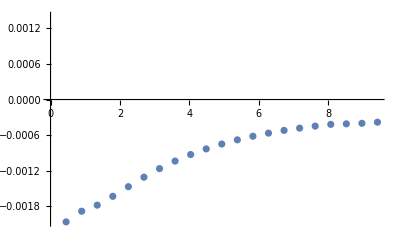

```mathematica
ListPlot[datak0]
```

```mathematica
datak0H=Select[datak0,#⟦1⟧≥ 4&];
fit=Fit[datak0H,1/x,x]
```

-0.0036229014802365964/x

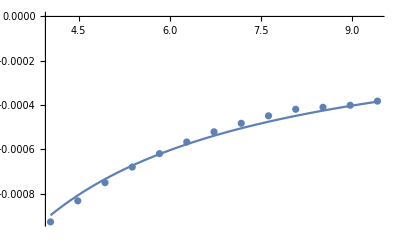

```mathematica
Show[ListPlot[datak0H],Plot[fit,{x,datak0H⟦1,1⟧,datak0H⟦-1,1⟧}]]
```